# Crash Course in Mathematica Basics

Christopher Hanusa (chanusa@qc.cuny.edu)
10 October 2017

## Getting started

Mathematica is Case - SenSitive (AA is not the same as aA), so be careful about what you type. In particular, all built - in Mathematica functions are spelled out and capitalized, such as Table, ListPlot, IntegerPart, etc.  Mathematica text changes color as you type so that you will know if a command or a variable is defined in the system.

Hover over a command to learn more.  Or browse the Documentation Center!

In Mathematica, it is important to distinguish between parentheses (), brackets [], and braces {} :

Parentheses () : Used to group mathematical expressions, such as (3 + 4)/(5 + 7).

Brackets [] : Used when calling functions, such as N[Pi].

Braces {} : Used when making lists, such as {i, 1, 20}.

If you use the wrong symbols in the wrong places or if you do not have a closing symbol for every opening symbol, Mathematica will give you an error message.

Newer versions of Mathematica have the suggestion bar, which helps you figure out other things you can do with an output, and gives a quick way to learn new commands.

```mathematica
Pi^2
```

(Note capital Pi since Mathematica-predefined!)  
REMEMBER: Use Shift-Enter to evaluate.

## Lists

In Mathematica, the key data structure is the list.  Whenever multiple numbers are to be grouped together into one object, this object will be a list.  For example, if you wish to reference the point (2,1) in the (x,y) plane, you would use write it as the list {2,1}.  Every list is surrounded by a left brace { and a right brace }.  Entries of the list are separated by commas.

Define a variable to be our list using = .  Since predefined Mathematica commands start with upper case letters, it is a good idea to use lower case letters for user-defined variable names.  #likeAHashTag

```mathematica
aList={{1,2},{2,3},{4,5}}
```

```mathematica
aList
```

Define a variable but suppress the output using a semicolon ; .

```mathematica
anotherList={1,2,3,5,8,13,21};
```

```mathematica
anotherList
```

## Table, Part I

The most important command to master at this early stage is the Table command.  This command will generate a list based on a function you specify.  
First, let's analyze the structure of a Table command:

```mathematica
Table[x^2,{x,0,5}]
```

There are always two inputs, a function (x^2) and a list ({x,0,5}) that specifies the values of x that will be inserted into the function. 
The first element in the list is always the variable that is modified by the function (in this case, x).  

[Notice that the variable is automatically colored teal in this list and in the function for your convenience.]

Depending on what the list contains, the values of this variable are specified in different ways.

If the list is of length three, such as {x,-1,5}, then the values of x that will be inserted are starting at the first number, ending at the second number.

```mathematica
Table[x^2,{x,-1,5}]
```

If the list is of length four, such as {x,0,10,2}, then the values of x that will be inserted are starting at the first number continuing until the second number by increments of the last number.

```mathematica
Table[x^2,{x,0,10,2}]
```

### More Incrementing Variables

The Table command can also create a list with two or more variables changing at a time.  Simply put two variable ranges as inputs.  In the following example, we consider all values of x from 1 to 6 and all values of y from 1 to 6 and multiply them together (because that's what the function x*y says to do).

```mathematica
array=Table[x*y,{x,6},{y,6}]
```

```mathematica
TableForm[array]
```

It is often a good idea to give the list of points you want to plot a descriptive name first (here I define the variable array).

The output to a Table command with multiple incrementing variables is a nested list.

### More POWER!

Your function can be of arbitrary type.  It can create coordinate pairs, graphics, ... anything that involves a variable!  (See more in the Documentation Center.)

```mathematica
Table[{x,x^2},{x,-3,0}]
```

```mathematica
Table[Style["text", s], {s, 10, 20}]
```

```mathematica
Table[Graphics[RegularPolygon[n],ImageSize->Tiny],{n,3,10}]
```

```mathematica
Table[KnotData[{"TorusKnot",{3,n}}],{n,5,11,3}]
```

### Comprehension Question

The command Prime[n] gives the n^th prime number
How would you create a list of the 4th, 9th, 14th, ... 99th prime number?

#### Solution

```mathematica
Table[Prime[n],{n,4,99,5}]
```

## A few of the many useful list commands

### Length

Length will tell you how many elements there are in the list.

```mathematica
Length[{1,2,3}]
```

```mathematica
Length[{1,{2,3}}]
```

### Parts of lists

It is often useful to single out one or more of the entries of a list.  For this we use double square brackets [[n]].

```mathematica
powersOfTen[[5]]
```

Note that unlike in some other languages, indices of lists start at 1.

When the list is a nested list, you can reference an entry (a sublist) or even an entry of the sublist.

```mathematica
nestedList={{1,2},{3,4},{5,6}};
```

```mathematica
nestedList[[2]]
```

```mathematica
nestedList[[2,1]]
```

### Flatten

When there are nested lists and you would like to remove some of the extra braces, you should use Flatten.

```mathematica
list=Table[x*y,{x,3},{y,3}]
```

```mathematica
Flatten[list]
```

You can also specify how many layers of braces you want to remove.

```mathematica
list2=Table[{x,y},{x,3},{y,3}]
```

```mathematica
Flatten[list2]
```

```mathematica
Flatten[list2,1]
```

### Append

When you want to add elements to the end of a preexisting list, use Append.

```mathematica
powersOfTen=Table[10^i,{i,0,5}]
```

```mathematica
Append[powersOfTen,10^6]
```

```mathematica
powersOfTen
```

You can see that powersOfTen does not change when using Append or Prepend. 
You need to redefine powersOfTen if you want to actually add an entry to the list for future use.

```mathematica
powersOfTen=Append[powersOfTen,10^6]
```

```mathematica
powersOfTen
```

## Map

An extremely important command is the Map command.  What Map[function,list] does is to take the function and evaluates the function at each entry of the list individually and returns the results in a list. For example, if you want to know the values of Sin[x] for multiples of Pi/6, you can Map the Sin function onto the desired list.

```mathematica
piList=Table[i,{i,0,2Pi,Pi/6}]
```

```mathematica
Map[Sin,piList]
```

More generically, if your list is {e1,e2,e3} and your function is fcn, then Map will return a list with fcn evaluated at each entry:

```mathematica
Map[fcn,{e1,e2,e3}]
```

The shorthand for Map is /@ (slash-at).

```mathematica
fcn/@{e1,e2,e3}
```

## Defining an unnamed function

Suppose you want to code in a function that you only want to apply once and you don’t want to worry about giving it a name.  Then you can create an unnamed function.  They are a bit confusing at first, but become very handy as you become proficient.

(RHS(#))&   or   (RHS(#1,#2))&

(RHS stands for Right Hand Side, and represents the actual function you want to apply to the variables.)

The # symbol represents an unnamed input variable. If your function has  more than one input, use #1, #2, #3, ... to represent the first, second, third, ... inputs in order.

The & symbol represents the end of the function and that signals to Mathematica that what follows should be the inputs to the function.

Often to increase readability, you can use parentheses ( ) to delimit the beginning and end of your unnamed function.

### Examples

This is a function that takes one input and squares it

```mathematica
#^2&
```

```mathematica
(#^2&)[Pi]
```

π^2

This is a function that takes two inputs and adds them.

```mathematica
(#1+#2)&[3,4]
```

7

Notice that when calling unnamed functions, you still need to use square brackets around the inputs.

### Unnamed functions and Map

An especially handy place to use unnamed functions is in tandem with the Map command. You might have a list of objects and want to apply a function to the whole list, but don’t especially want to define the function outright.  You can use the Map command and an unnamed function to do it!

Here is an example that squares all the entries in a list.

```mathematica
mylist=Table[i,{i,4,20,3}]
Map[#^2&,mylist]
```

{4,7,10,13,16,19}

{16,49,100,169,256,361}

And here is an example that creates regular polygons with the number of sides of the entries in the list.


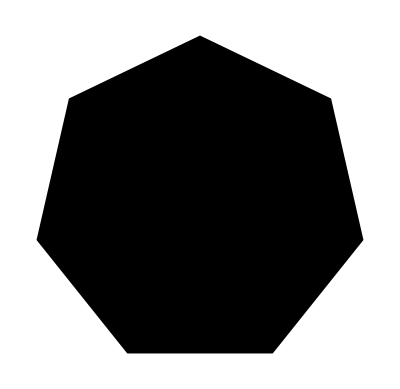
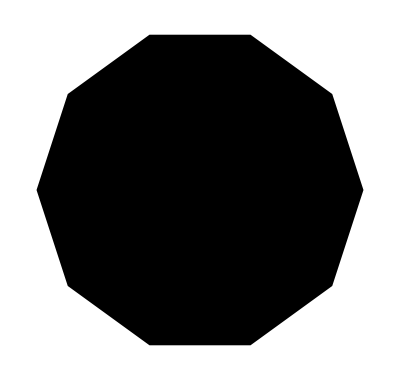
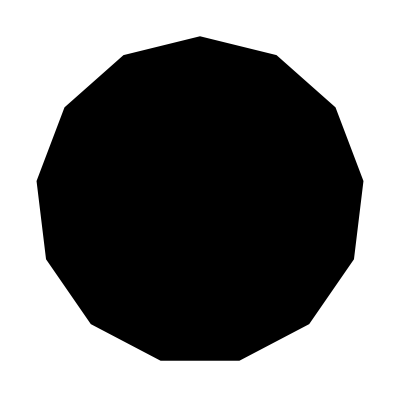
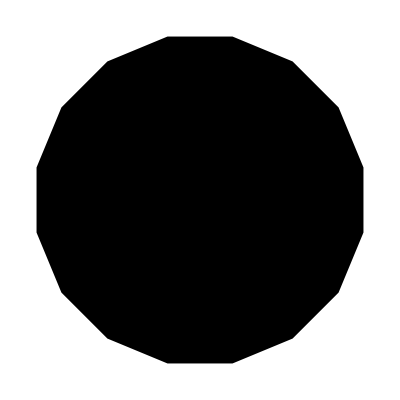
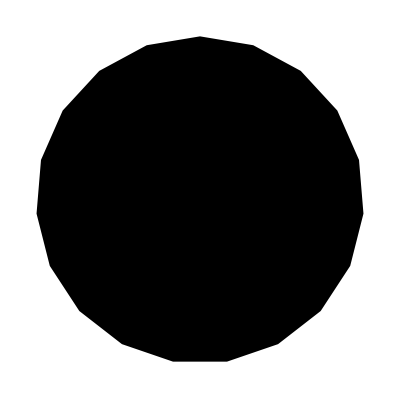

```mathematica
Map[Graphics[RegularPolygon[#]]&, mylist]
```

In the next notebook we’ll be creating spheres centered at various points.  The syntax is

```mathematica
?Sphere
```

Sphere[p] represents a unit sphere centered at the point p.
Sphere[p,r] represents a sphere of radius r centered at the point p.
Sphere[{p_1,p_2,…},r] represents a collection of spheres of radius r.

```mathematica
Graphics3D[{Sphere[{0,0,0},.2],Sphere[{1,1,1},.2],Sphere[{2,2,2},.2],Sphere[{3,3,3},.2]}]
```

-Graphics3D-

Instead we can use Table and Map:

```mathematica
coords=Table[{i,i,i},{i,0,3}]
balls=Map[Sphere[#,.2]&,coords]
Graphics3D[balls]
```

{{0,0,0},{1,1,1},{2,2,2},{3,3,3}}

{Sphere[{0,0,0},0.2],Sphere[{1,1,1},0.2],Sphere[{2,2,2},0.2],Sphere[{3,3,3},0.2]}

-Graphics3D-

Which lets us do something much bigger!

```mathematica
coords=Flatten[Table[{i,j,k},{i,0,3},{j,0,3},{k,0,3}],2];
balls=Map[Sphere[#,.2]&,coords];
Graphics3D[balls]
```

-Graphics3D-

## Adding Randomness

To incorporate randomness, use RandomInteger or RandomReal. In both cases, the first input gives the range in which to choose the random number; a second input tells how many of such numbers to make, if more than one is desired.

```mathematica
RandomInteger[{-4,4}]
RandomInteger[{1,10},40]
```

You can even specify that you would like tuples of numbers.  Here we have random (x,y) coordinates with both x and y in the range [0,1].

```mathematica
RandomReal[0.5]
RandomReal[{0,1},{10,2}]
```

Here we simulate 400 rolls of a die:

```mathematica
rolls=RandomInteger[{1,6},400];
Sort[Tally[rolls]]
Histogram[rolls]
```

## User-defined functions

f[x_,y_] := RHS

(RHS stands for Right Hand Side.)

f is the coder-specified name of the function.  Since all built-in Mathematica functions start with a capital letter, it’s good practice to start user-defined functions with a lower case letter.  To use multiple-word function names, captialize it #likeAHashtag.

All functions use square brackets [] to mark the beginning and end of the inputs.

Inside the square brackets, you give coder-specified names to each of the variables since you will be using them on the Right Hand Side of the definition when you code what the function does.

When you define these variables, use an underscore _ to tell Mathematica that the input for this variable can be any one thing. (One number, One list, One shape, ... anything!)  This is the simplest type of a “pattern” in Mathematica.

Unlike defining variables and using the = operator, when you define a function you use the := operator.  It is called “SetDelayed” because it means that every time you evaluate the left hand side (When you call the function), it RE-evaluates the Right Hand Side.

### Simple function example

Define a function that takes as an input a number and outputs its square.

```mathematica
squareMe[x_]:=x^2
```

```mathematica
squareMe[-6]
```

Notice that Mathematica colors the coder-defined variables in the definition green. If you had made a mistake and not included the underscore, the color would be different:

```mathematica
squareMe[x]:=x^2
```

### Simple function with more than one variable

Define a function that takes as an input a list of two numbers and outputs its sum.

```mathematica
addEmUp[{x_,y_}]:=x+y
```

```mathematica
addEmUp[{3,-10}]
```

Notice that we did not specify that x and y had to be numbers.  Mathematica will add together whatever you put as inputs, even if the sum can’t be simplified.

```mathematica
addEmUp[{{2,3},{9,-10}}]
```

```mathematica
addEmUp[{Red,Orange}]
```

```mathematica
addEmUp[{"Hello","Goodbye"}]
```

### Comprehension Question

A) Create a list of the points on the curve y=x^2 for integers 0 through 10.
B) Use Map and the addEmUp function to calculate x+x^2 for integers 0 through 10.

#### Solution

```mathematica
points=Table[{x,x^2},{x,0,10}]
```

```mathematica
Map[addEmUp,points]
```